# DECONVOLUTION

## ELE 489: DIGITAL SIGNAL PROCESSING LABORATORY

Heath Buchanan/ Taylor Brookes

Due date: 2/21/23

## Introduction

In our previous lab, we experimented with the concept of convolution. Convolution is a mathematical method of combining two signals to form a third. The concept of convolution is used to determine the response of a system at rest to a unit impulse, step, or other input signal. We did this by using the principles of linearity and superposition to calculate the responses and demonstrated this using the Wolfram Language code in Figure 1. For this lab, we were introduced to deconvolution. Given two finite-length sequences y and h, where y is the result of convolution between h and an some unknown sequence x , we were tasked with developing the code to perform deconvolution to discover the values of the sequence x. To do this, we used short sequences and our previously developed convolution function in Lab 1 to obtain samples of y and used it to reconstruct samples of x. We then continue by comparing our results to results using the built-in Wolfram Language function ListDeconvolve.

#### Figure 1

This is our convolution code from Lab 1.

```mathematica
convolve[x_,h_] := Module[{lenX,lenH,table,i,k,l,m,total},
lenX =  Length [x];
lenH = Length[h];
table = Table[0, {lenX-lenH+1}];
For[l = lenH, l<=lenX,l++,i = 1; k=l;total = 0;
For[m = 1, m <=lenH, m++,total +=h[[m]]*x[[k]]; k--; i++];
table [[l-lenH+1]]= total
]
;table]
```

For the preliminaries, we made a couple lists and then performed a convolution and deconvolution using the Wolfram Language ListConvolve and ListDeconvolve functions, respectively. Here, you can see that the ListConvolve function does not produce all the values in the y list, only the steady-state values. In the ListDeconvolve method, the x list is padded with zeroes.

```mathematica
x  := {19,7,4,16,9,14,19,11};
y := {323,480,562,880,680,797,1096,1003,864,608,231};
h := {17,19,19,21};
```

```mathematica
ListConvolve[h,x]
```

{880,680,797,1096,1003}

```mathematica
ListDeconvolve[h,y,Method->{"DampedLS",0.00}]
```

{-2.76546×10^-15,-1.33428×10^-15,19.,7.,4.,16.,9.,14.,19.,11.,1.54169×10^-14}

## Problem 1. Code development

For problem 1, we implemented the deconvolution calculation using  nested For loops and an if statement to differentiate between values produced before or after all of the h values are used within the function. A description of variables can be found below.

lenY is length of Y list
lenH is length of H list
table is the output list of X
L is x index
j is h index
i is x index for adding
	we add from right to left
	(h3x1 + h2hx2) = hxSum
	x3 = (y3 - hxSum) / h1
total is the value to add to the X list
hxSum is the sum of each h * x, which is then subtracted from the y and divided by h1

```mathematica
deconvolve[y_,h_] := Module[{lenY, lenH, table, i,j,l,total,hxSum},
lenY = Length[y];
lenH = Length[h];
hxSum = 0;
total = 0;
table = Table[0,{lenY - lenH + 1}];
For[l = 1,l<=(lenY - lenH + 1),l++,
If[l<lenH,
For[j=l;i=1,j>1,j--;i++,hxSum+=h[[j]]*table[[i]]],
For[j=lenH;i=l-lenH+1,j>1,j--;i++,hxSum+=h[[j]]*table[[i]]];
];
total = (y[[l]]-hxSum)/h[[1]];hxSum=0;
table[[l]]=total
]
;table//N]
```

The next step was to run the code to see if it worked.

```mathematica
deconvolve[y,h]
```

{19.,7.,4.,16.,9.,14.,19.,11.}

After we got some code working, we used our previously generated lists to perform an analysis of our results.

```mathematica
y := {323,480,562,880,680,797,1096,1003,864,608,231};
h := {17,19,19,21};
x :=deconvolve[y,h];
```

We then test our results against the ListDeconvolve.

```mathematica
ListDeconvolve[h,y,Method->{"DampedLS",0.00}]
```

{-2.76546×10^-15,-1.33428×10^-15,19.,7.,4.,16.,9.,14.,19.,11.,1.54169×10^-14}

As you can see, our results match the results from ListDeconvolve. We then convolve our solution x  with h to see if we can return y. In fact, we do.

```mathematica
convolve[x, h]
```

{880.,680.,797.,1096.,1003.}

Our convolve function only returns the steady-state values from the list y.

## Problem 2.

For the next step, we were to use our deconvolution function to deconvolve the sequence shown below using the following filter h:

```mathematica
h={1,1,1,1,1,1,1}/7.;
```

This defines sequence y:

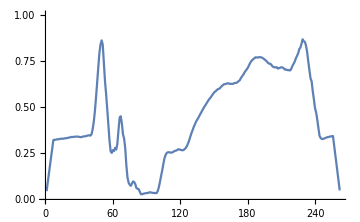

```mathematica
y=;
ListLinePlot[y,PlotRange->{0,1},ImageSize->Medium]
```

Our first step was to use our deconvolution function to find x.

```mathematica
deconvolve[y,h]
x = %;
```

{0.313725,0.329412,0.317647,0.32549,0.32549,0.309804,0.32549,0.329412,0.329412,0.329412,0.333333,0.32549,0.32549,0.329412,0.329412,0.329412,0.345098,0.333333,0.333333,0.337255,0.337255,0.337255,0.345098,0.341176,0.341176,0.337255,0.341176,0.341176,0.333333,0.337255,0.329412,0.345098,0.352941,0.34902,0.345098,0.341176,0.34902,0.34902,0.341176,0.345098,0.4,0.537255,0.623529,0.74902,0.87451,0.894118,0.921569,0.94902,0.858824,0.784314,0.588235,0.172549,0.203922,0.435294,0.372549,0.270588,0.188235,0.188235,0.105882,0.305882,0.4,0.498039,0.203922,0.403922,0.705882,0.572549,0.368627,0.133333,0.0784314,0.0470588,0.0470588,0.054902,0.105882,0.172549,0.0509804,0.0392157,0.137255,0.121569,0.0313725,0.0235294,0.0235294,0.027451,0.027451,0.0392157,0.027451,0.027451,0.0392157,0.0392157,0.0313725,0.0392157,0.0392157,0.0431373,0.0431373,0.027451,0.027451,0.027451,0.0392157,0.0313725,0.0470588,0.121569,0.180392,0.231373,0.25098,0.25098,0.270588,0.262745,0.243137,0.254902,0.254902,0.25098,0.243137,0.262745,0.27451,0.270588,0.278431,0.270588,0.262745,0.278431,0.266667,0.25098,0.266667,0.266667,0.282353,0.301961,0.317647,0.345098,0.34902,0.384314,0.407843,0.407843,0.415686,0.435294,0.443137,0.447059,0.462745,0.47451,0.490196,0.494118,0.513725,0.521569,0.521569,0.533333,0.541176,0.556863,0.564706,0.572549,0.572549,0.584314,0.592157,0.603922,0.596078,0.6,0.615686,0.596078,0.6,0.639216,0.65098,0.631373,0.635294,0.619608,0.607843,0.619608,0.635294,0.631373,0.635294,0.631373,0.619608,0.635294,0.627451,0.639216,0.658824,0.67451,0.662745,0.701961,0.698039,0.686275,0.713725,0.729412,0.72549,0.72549,0.784314,0.788235,0.760784,0.764706,0.768627,0.760784,0.760784,0.780392,0.780392,0.776471,0.768627,0.756863,0.74902,0.729412,0.74902,0.745098,0.737255,0.717647,0.721569,0.745098,0.698039,0.686275,0.717647,0.721569,0.717647,0.72549,0.694118,0.713725,0.701961,0.737255,0.713725,0.690196,0.67451,0.698039,0.690196,0.701961,0.72549,0.713725,0.764706,0.780392,0.768627,0.780392,0.819608,0.815686,0.811765,0.917647,0.847059,0.909804,0.94902,0.745098,0.792157,0.670588,0.67451,0.490196,0.584314,0.635294,0.631373,0.415686,0.368627,0.337255,0.32549,0.313725,0.329412,0.32549,0.329412,0.333333,0.333333,0.341176,0.333333,0.345098,0.345098,0.333333,0.34902,0.341176,0.34902,0.341176}

We then check our results using ListDeconvolve.

```mathematica
ListDeconvolve[h,y,Method->{"DampedLS",0.00}]
```

{5.87317×10^-15,-2.10592×10^-14,1.18426×10^-14,0.313725,0.329412,0.317647,0.32549,0.32549,0.309804,0.32549,0.329412,0.329412,0.329412,0.333333,0.32549,0.32549,0.329412,0.329412,0.329412,0.345098,0.333333,0.333333,0.337255,0.337255,0.337255,0.345098,0.341176,0.341176,0.337255,0.341176,0.341176,0.333333,0.337255,0.329412,0.345098,0.352941,0.34902,0.345098,0.341176,0.34902,0.34902,0.341176,0.345098,0.4,0.537255,0.623529,0.74902,0.87451,0.894118,0.921569,0.94902,0.858824,0.784314,0.588235,0.172549,0.203922,0.435294,0.372549,0.270588,0.188235,0.188235,0.105882,0.305882,0.4,0.498039,0.203922,0.403922,0.705882,0.572549,0.368627,0.133333,0.0784314,0.0470588,0.0470588,0.054902,0.105882,0.172549,0.0509804,0.0392157,0.137255,0.121569,0.0313725,0.0235294,0.0235294,0.027451,0.027451,0.0392157,0.027451,0.027451,0.0392157,0.0392157,0.0313725,0.0392157,0.0392157,0.0431373,0.0431373,0.027451,0.027451,0.027451,0.0392157,0.0313725,0.0470588,0.121569,0.180392,0.231373,0.25098,0.25098,0.270588,0.262745,0.243137,0.254902,0.254902,0.25098,0.243137,0.262745,0.27451,0.270588,0.278431,0.270588,0.262745,0.278431,0.266667,0.25098,0.266667,0.266667,0.282353,0.301961,0.317647,0.345098,0.34902,0.384314,0.407843,0.407843,0.415686,0.435294,0.443137,0.447059,0.462745,0.47451,0.490196,0.494118,0.513725,0.521569,0.521569,0.533333,0.541176,0.556863,0.564706,0.572549,0.572549,0.584314,0.592157,0.603922,0.596078,0.6,0.615686,0.596078,0.6,0.639216,0.65098,0.631373,0.635294,0.619608,0.607843,0.619608,0.635294,0.631373,0.635294,0.631373,0.619608,0.635294,0.627451,0.639216,0.658824,0.67451,0.662745,0.701961,0.698039,0.686275,0.713725,0.729412,0.72549,0.72549,0.784314,0.788235,0.760784,0.764706,0.768627,0.760784,0.760784,0.780392,0.780392,0.776471,0.768627,0.756863,0.74902,0.729412,0.74902,0.745098,0.737255,0.717647,0.721569,0.745098,0.698039,0.686275,0.717647,0.721569,0.717647,0.72549,0.694118,0.713725,0.701961,0.737255,0.713725,0.690196,0.67451,0.698039,0.690196,0.701961,0.72549,0.713725,0.764706,0.780392,0.768627,0.780392,0.819608,0.815686,0.811765,0.917647,0.847059,0.909804,0.94902,0.745098,0.792157,0.670588,0.67451,0.490196,0.584314,0.635294,0.631373,0.415686,0.368627,0.337255,0.32549,0.313725,0.329412,0.32549,0.329412,0.333333,0.333333,0.341176,0.333333,0.345098,0.345098,0.333333,0.34902,0.341176,0.34902,0.341176,7.6596×10^-15,-3.39543×10^-15,1.45009×10^-15}

Finally, we use our convolve function to test our results against y, then plot them on a ListLinePlot.

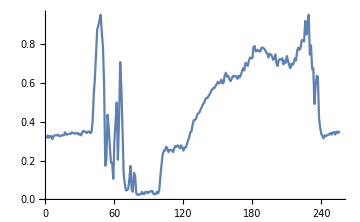

```mathematica
ListLinePlot[{x}, ImageSize ->Medium]
```

As we can see we returned the correct output, however it is distorted quite a bit. This is due to the fact that the x values must be convolved with the h values to produce the smooth y graph.

## Problem 3.

Perfect reconstruction is only possible if the distortion, meaning the convolution filter h, is known exactly. However, in practice this is never the case. This is when deconvolution becomes an interesting problem.

In this problem reconstruct the signal in Problem 2 using the following and comment on the results. Do any of the following return a result that is close to the original x? Which one gives the best result? Anything surprising to note?

```mathematica
h1={1,1,1,1,1}/5.;
```

```mathematica
h2={0.95,1,1,1,1,1,0.95}/7.;
```

```mathematica
h3={0.85,1,1,1,1,1,0.85}/7.;
```

```mathematica
h4={0.5,1,1,1,1,1,0.5}/7.;
```

```mathematica
h5=GaussianMatrix[{{2}}];
```

We know our code works, so our last step was to implement deconvolution for each h[n] above and plot the results.

For h1:

```mathematica
deconvolve[y,h1];
x1 = %;
ListLinePlot[{Labeled[y, "output y"],Labeled[x1, "deconvolution with h1"]}, PlotLayout -> "Row", ImageSize -> Large]
```

-Graphics-

For h2:

```mathematica
deconvolve[y,h2];
x2 = %;
ListLinePlot[{Labeled[y, "output y"],Labeled[x2, "deconvolution with h2"]}, PlotLayout -> "Row", ImageSize -> Large]
```

-Graphics-

For h3:

```mathematica
deconvolve[y,h3];
x3 = %;
ListLinePlot[{Labeled[y, "output y"],Labeled[x3, "deconvolution with h3"]}, PlotLayout -> "Row", ImageSize -> Large]
```

-Graphics-

For h4:

```mathematica
deconvolve[y,h4];
x4 = %;
ListLinePlot[{Labeled[y, "output y"],Labeled[x4, "deconvolution with h4"]}, PlotLayout -> "Row", ImageSize -> Large]
```

-Graphics-

For h5:

```mathematica
deconvolve[y,h5];
x5 = %;
ListLinePlot[{Labeled[y, "output y"],Labeled[x5, "deconvolution with h5"]}, PlotLayout -> "Row",  ImageSize -> Large]
```

-Graphics-

It is clear that filter h2 is the closest result to the original x value. There are some trends that we see throughout the deconvolution function, though. We notice that the peaks of the deconvolution graphs occur at length[h] intervals, which we deduce has something to do with the period. We believe this is a form of aliasing. In addition, the smaller the edges of the h[n] lists, the higher the amplitude of our graphs. For filters h4 and h5, its not clear what they are doing, but we can see that they drastically change at ~170 for some reason. We actually modified filter h4 by a very small amount to see if we noticed a large difference:

```mathematica
h4a={0.51,1,1,1,1,1,0.51}/7.;
deconvolve[y,h4a];
x4a = %;
ListLinePlot[{Labeled[y, "output y"],Labeled[x4a, "deconvolution with h4"]}, PlotLayout -> "Row", ImageSize -> Large]
```

-Graphics-

Notice this returns a noticeably more recognizable output signal y compared to the resulting input signal x. We then tired the same method for h5.

```mathematica
h5a=GaussianMatrix[{{33}}];
deconvolve[y,h5a];
x5a = %;
ListLinePlot[{Labeled[y, "output y"],Labeled[x5a, "deconvolution with h5"]}, PlotLayout -> "Row",  ImageSize -> Large]
```

-Graphics-

This result makes me think the filter takes any input signal x and turns it into a constant output. The amplitude of the highest point of y remains to be approximately 1, while the amplitude of the deconvolution spikes to around +/- 40, which is near to the 33 we input.

#### Conclusion

Deconvolution is the inverse operation of convolution. In signal processing, deconvolution is primarily used to recover the original signal after it has traveled through a filter (convolution) within some percentage error. Deconvolution is used in many practical applications, such as image deblurring, restoration of noisy images, and denoising of signals. Deconvolution methods have been developed to address different scenarios, such as blind deconvolution where the kernel is unknown, and non-linear deconvolution where the relationship between the input and output signals is not linear. We were shown that deconvolution can amplify noise and artifacts, leading to inaccurate results.
	In this lab, we developed a working code using our convolution function made in Lab 1. We were given two finite-length sequences y and h, where y is the result of convolution between h and an some unknown sequence x. Using our under-defined function deconvolve, we were able to successful implement deconvolution on a few examples and test it against the Wolfram Language ListDeconvolve function. For our first test, we were given a filter h and sequence y in order to return the original signal. We were able to return the original signal and found that our filter h had smoothed it for us.
	For the next section, we were given five different filters and an output to deconvolve to discover the original signal. For filters h1, h2, and h3, it was pretty clear to notice that the filters more or less averaged out the original signal. However, filters h4 and h5 proved to be a little more unintuitive. Filter h4 was a little tough to figure out. Filter h5 seemed to take a signal with a very high amplitude and squish it down to what essentially appears as a constant output.